# Space Debris (Model H); color scheme : -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["Space-Debris-Model.nb",InsertResults->False];
myThickness=0.005;tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,.015}][##]&;
```

## global parameters

```mathematica
(***   b , sL , sR , betL , betR , tauL , tauR : benefit parameters                      ***)
(***   a , tauC , betC , sC                    : cost parameters                         ***)
(***   Ts                                      : s-time-scale parameter                  ***)
(***   rlim , λ , inov , α (efficiency)        : Ṡ parameters (λ is dummy)               ***)
rLIM =0.155; iNOV=0.845; α = 0.25; tLIM=360;
nGRID=100;dGRID=0.01;intervalWIDTH=40;pGOAL=40;
```

## Figure 3A

-----------------------------------------------------------------------------

------------------ CHANGE PARAMETERS CALLED ---------------------------------

-----------------------------------------------------------------------------

Parameters used for benefit(s) :

b    :  0.85

s_L   :  0.

s_R   :  0.

β_L   :  60.

τ_L   :  0.4

β_R   :  10.

τ_R   :  2.

-------------------------------

Parameters used for cost(s) :

c    :  1

a    :  0.

s_c   :  0.15

β_c   :  5.

τ_c   :  0.1

-------------------------------

Parameters used for Ṡ(s,x)) :

T_s   :  1.

r_LIM  :  0.155

λ    :  0.

i_NOV  :  0.845

α ≡ ϵ :  0.25

-----------------------------------------------------------------------------

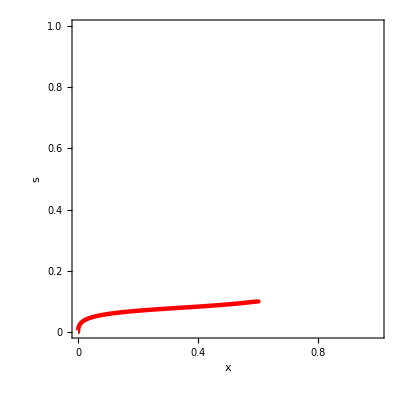

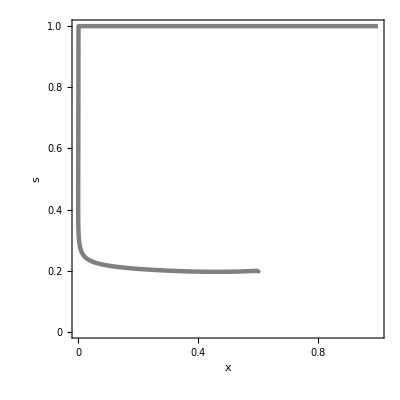

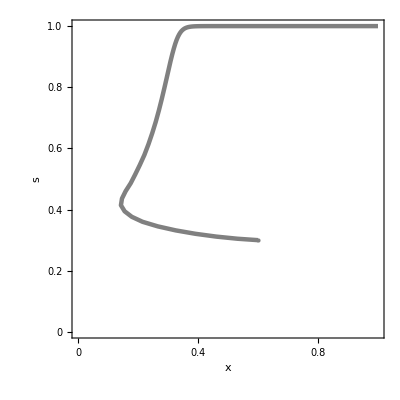

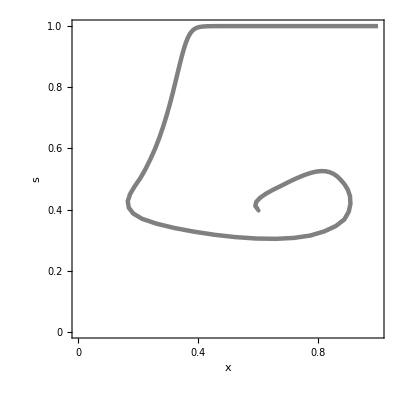

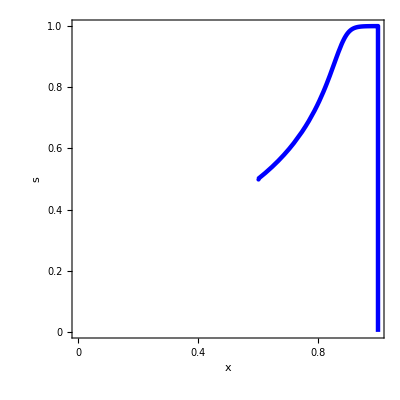

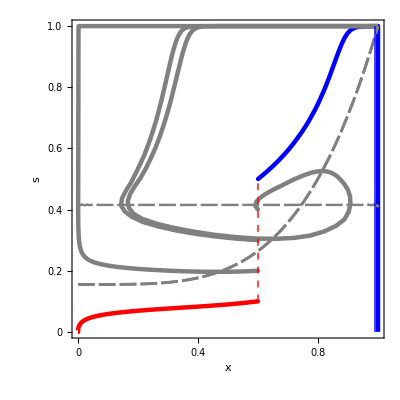

```mathematica
(***                                                                                     ***)
(***            plot parametric time evolution starting from x = 0.6 AND 0.1 < s < 0.5   ***)
(***                                                                                     ***)
GlobalRootNumber=1;
LoadParameters[0,GlobalRootNumber];
ChangeParameters[0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,rLIM,0.0,iNOV,α ];
q0=PlotRootsSimplex[0];
dataRed={{0.60,0.10}};
dataGray={{0.60,0.20},{0.60,0.30},{0.60,0.40}};
dataBlue={{0.60,0.50}};
(*   x = 0.60 && s = 0.10 *)
filX="dfig3/data-x-0.60-0.10-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.10-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Red;kol=Red;x0=0.60;s0=0.10;
q1=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q1]
(*   x = 0.60 && s = 0.20 *)
filX="dfig3/data-x-0.60-0.20-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.20-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Gray;kol=Gray;x0=0.60;s0=0.20;
q2=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q2]
(*   x = 0.60 && s = 0.30 *)
filX="dfig3/data-x-0.60-0.30-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.30-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Gray;kol=Gray;x0=0.60;s0=0.30;
q3=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q3]
(*   x = 0.60 && s = 0.40 *)
filX="dfig3/data-x-0.60-0.40-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.40-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Gray;kol=Gray;x0=0.60;s0=0.40;
q4=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q4]
(*   x = 0.60 && s = 0.50 *)
filX="dfig3/data-x-0.60-0.50-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.50-grid-1-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Blue;kol=Blue;x0=0.60;s0=0.50;
q5=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q5]
pl1=Show[q1,q3,q5,q0(*,Epilog->{{PointSize[Large],Red,Point[data1]},{Dashed,Red,Line[{{0.6,0.1},{0.6,0.50}}]}}*)];
pl2=Show[q2,q4,q0(*,Epilog->{{PointSize[Large],Blue,Point[data2]}*)(*,{Dashed,Blue,Line[{{0.9,0},{0.9,0.50}}]}}*)];
pltl=Show[pl1,pl2,
Epilog->{{PointSize[Large],Blue,Point[dataBlue]},{PointSize[Large],Gray,Point[dataGray]},{PointSize[Large],Red,Point[dataRed]},{Thick,Blue,Line[{{0.99,0.0},{0.99,1.0}}]},{Dashed,Red,Line[{{0.60,0.1},{0.60,0.5}}]}}
];
Show[pltl]
```

## Figure 3B

-----------------------------------------------------------------------------

------------------ CHANGE PARAMETERS CALLED ---------------------------------

-----------------------------------------------------------------------------

Parameters used for benefit(s) :

b    :  0.59

s_L   :  0.

s_R   :  0.

β_L   :  24.

τ_L   :  0.3

β_R   :  24.

τ_R   :  0.75

-------------------------------

Parameters used for cost(s) :

c    :  1

a    :  0.

s_c   :  0.05

β_c   :  5.

τ_c   :  0.1

-------------------------------

Parameters used for Ṡ(s,x)) :

T_s   :  1.

r_LIM  :  0.155

λ    :  0.

i_NOV  :  0.845

α ≡ ϵ :  0.25

-----------------------------------------------------------------------------

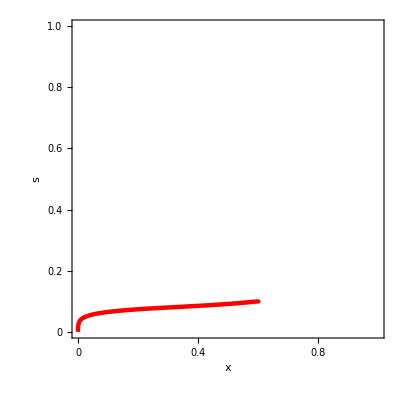

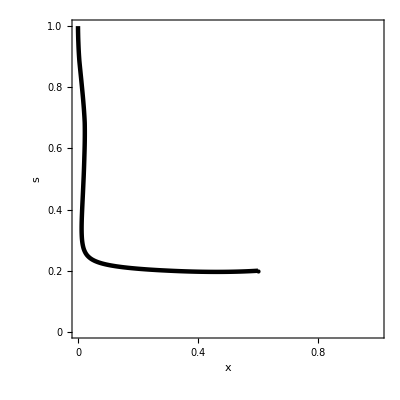

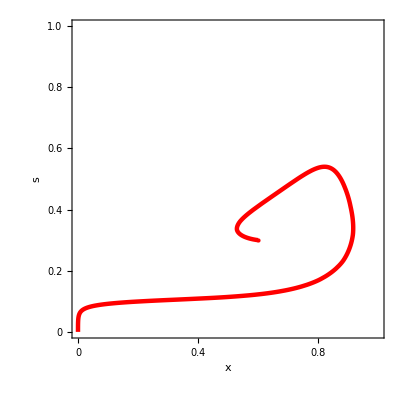

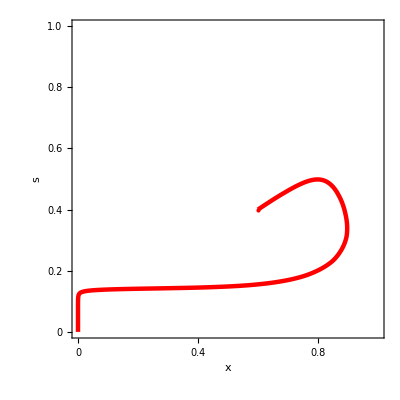

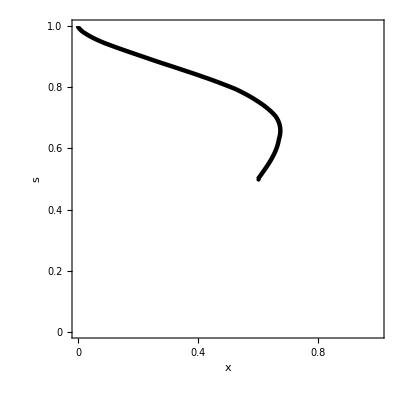

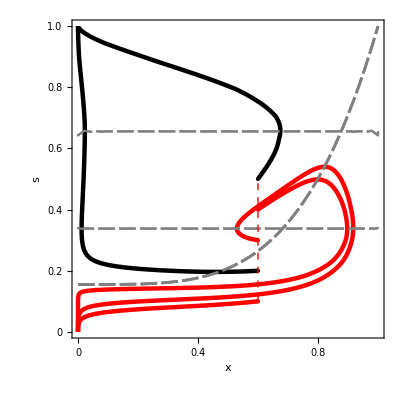

```mathematica
(***                                                                                     ***)
(***            plot parametric time evolution starting from x = 0.6 AND 0.1 < s < 0.5   ***)
(***                                                                                     ***)
GlobalRootNumber=2;
LoadParameters[0,GlobalRootNumber];
ChangeParameters[0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,rLIM,0.0,iNOV,α ];
q0=PlotRootsSimplex[0];
dataRed={{0.60,0.10},{0.60,0.30},{0.60,0.40}};
dataBlack={{0.60,0.20},{0.60,0.50}};

(*   x = 0.60 && s = 0.10 *)
filX="dfig3/data-x-0.60-0.10-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.10-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Red;kol=Red;x0=0.60;s0=0.10;
q1=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q1]
(*   x = 0.60 && s = 0.20 *)
filX="dfig3/data-x-0.60-0.20-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.20-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Black;kol=Black;x0=0.60;s0=0.20;
q2=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q2]
(*   x = 0.60 && s = 0.30 *)
filX="dfig3/data-x-0.60-0.30-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.30-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Red;kol=Red;x0=0.60;s0=0.30;
q3=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q3]
(*   x = 0.60 && s = 0.40 *)
filX="dfig3/data-x-0.60-0.40-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.40-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Red;kol=Red;x0=0.60;s0=0.40;
q4=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q4]
(*   x = 0.60 && s = 0.50 *)
filX="dfig3/data-x-0.60-0.50-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.50-grid-2-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Black;kol=Black;x0=0.60;s0=0.50;
q5=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q5]
pl1=Show[q1,q3,q5,q0(*,Epilog->{{PointSize[Large],Red,Point[data1]},{Dashed,Red,Line[{{0.6,0.1},{0.6,0.50}}]}}*)];
pl2=Show[q2,q4,q0(*,Epilog->{{PointSize[Large],Blue,Point[data2]}*)(*,{Dashed,Blue,Line[{{0.9,0},{0.9,0.50}}]}}*)];
pltr=Show[pl1,pl2,Epilog->{{PointSize[Large],Black,Point[dataBlack]},{PointSize[Large],Red,Point[dataRed]},{Dashed,Red,Line[{{0.60,0.1},{0.60,0.5}}]}}];
Show[pltr]
```

## Figure 3C

-----------------------------------------------------------------------------

------------------ CHANGE PARAMETERS CALLED ---------------------------------

-----------------------------------------------------------------------------

Parameters used for benefit(s) :

b    :  1.

s_L   :  0.2

s_R   :  0.

β_L   :  40.

τ_L   :  0.4

β_R   :  10.

τ_R   :  2.

-------------------------------

Parameters used for cost(s) :

c    :  1

a    :  0.1

s_c   :  0.35

β_c   :  75.

τ_c   :  0.4

-------------------------------

Parameters used for Ṡ(s,x)) :

T_s   :  1.

r_LIM  :  0.155

λ    :  0.

i_NOV  :  0.845

α ≡ ϵ :  0.25

-----------------------------------------------------------------------------

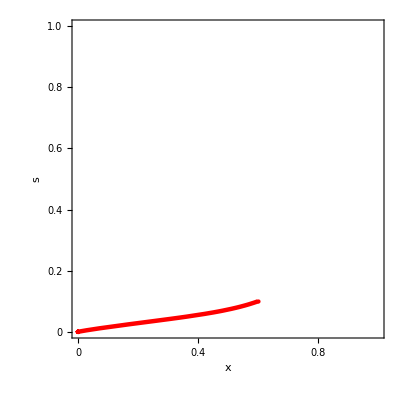

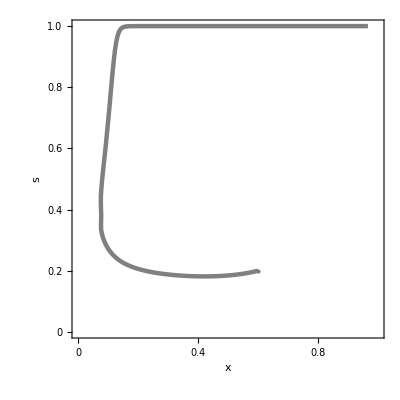

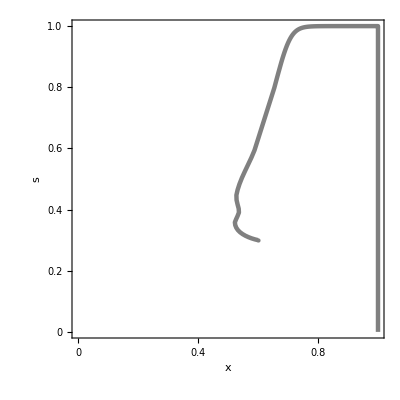

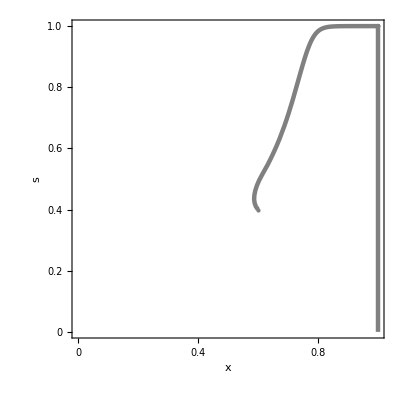

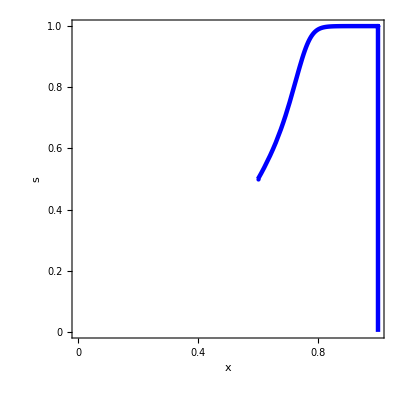

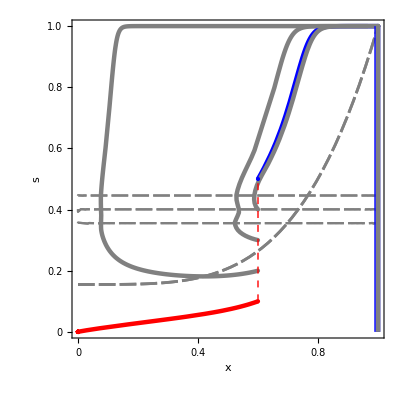

```mathematica
(***                                                                                     ***)
(***            plot parametric time evolution starting from x = 0.6 AND 0.1 < s < 0.5   ***)
(***                                                                                     ***)
GlobalRootNumber=3;
LoadParameters[0,GlobalRootNumber];
ChangeParameters[0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,rLIM,0.0,iNOV,α ];
q0=PlotRootsSimplex[0];
dataRed={{0.60,0.10}};
dataGray={{0.60,0.20},{0.60,0.30},{0.60,0.40}};
dataBlue={{0.60,0.50}};
(*   x = 0.60 && s = 0.10 *)
filX="dfig3/data-x-0.60-0.10-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.10-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Red;kol=Red;x0=0.60;s0=0.10;
q1=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q1]
(*   x = 0.60 && s = 0.20 *)
filX="dfig3/data-x-0.60-0.20-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.20-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Gray;kol=Gray;x0=0.60;s0=0.20;
q2=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q2]
(*   x = 0.60 && s = 0.30 *)
filX="dfig3/data-x-0.60-0.30-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.30-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Gray;kol=Gray;x0=0.60;s0=0.30;
q3=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q3]
(*   x = 0.60 && s = 0.40 *)
filX="dfig3/data-x-0.60-0.40-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.40-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Gray;kol=Gray;x0=0.60;s0=0.40;
q4=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q4]
(*   x = 0.60 && s = 0.50 *)
filX="dfig3/data-x-0.60-0.50-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.50-grid-3-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Blue;kol=Blue;x0=0.60;s0=0.50;
q5=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q5]
pl1=Show[q1,q3,q5,q0(*,Epilog->{{PointSize[Large],Red,Point[data1]},{Dashed,Red,Line[{{0.6,0.1},{0.6,0.50}}]}}*)];
pl2=Show[q2,q4,q0(*,Epilog->{{PointSize[Large],Blue,Point[data2]}*)(*,{Dashed,Blue,Line[{{0.9,0},{0.9,0.50}}]}}*)];
plbl=Show[pl1,pl2,Epilog->{{PointSize[Large],Blue,Point[dataBlue]},{PointSize[Large],Gray,Point[dataGray]},{PointSize[Large],Red,Point[dataRed]},{Thick,Blue,Line[{{0.99,0.0},{0.99,1.0}}]},{Dashed,Red,Line[{{0.60,0.1},{0.60,0.5}}]}}];
Show[plbl]
```

## Figure 3D

-----------------------------------------------------------------------------

------------------ CHANGE PARAMETERS CALLED ---------------------------------

-----------------------------------------------------------------------------

Parameters used for benefit(s) :

b    :  1.

s_L   :  0.05

s_R   :  0.

β_L   :  20.

τ_L   :  0.4

β_R   :  20.

τ_R   :  0.75

-------------------------------

Parameters used for cost(s) :

c    :  1

a    :  0.1

s_c   :  0.15

β_c   :  55.

τ_c   :  0.35

-------------------------------

Parameters used for Ṡ(s,x)) :

T_s   :  1.

r_LIM  :  0.155

λ    :  0.

i_NOV  :  0.845

α ≡ ϵ :  0.25

-----------------------------------------------------------------------------

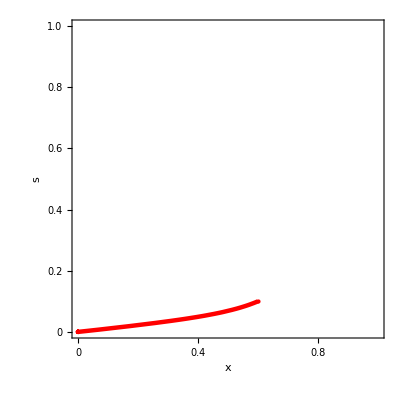

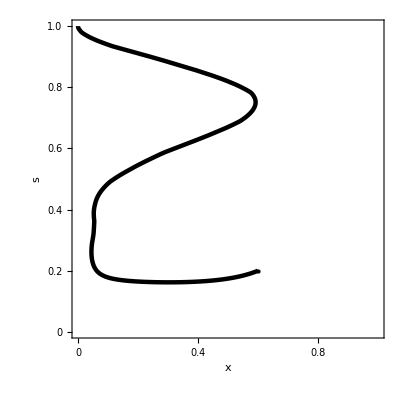

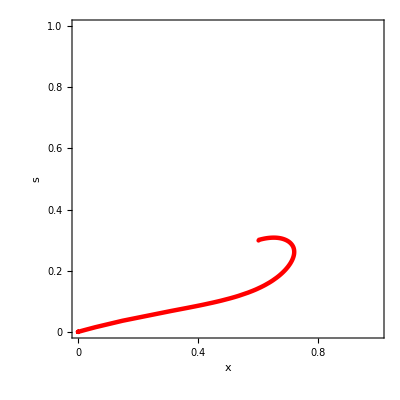

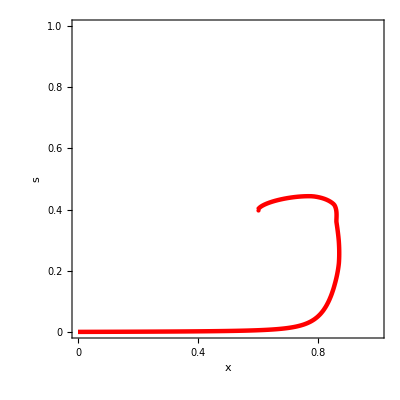

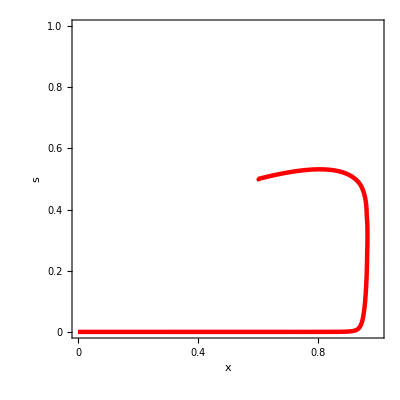

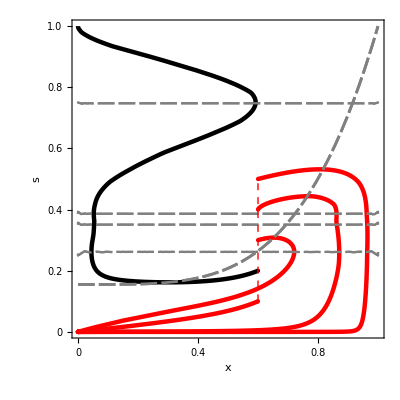

```mathematica
(***                                                                                     ***)
(***            plot parametric time evolution starting from x = 0.6 AND 0.1 < s < 0.5   ***)
(***                                                                                     ***)
GlobalRootNumber=4;
LoadParameters[0,GlobalRootNumber];
ChangeParameters[0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,rLIM,0.0,iNOV,α ];
q0=PlotRootsSimplex[0];
dataRed={{0.60,0.10},{0.60,0.30},{0.60,0.40},{0.60,0.50}};
dataBlack={{0.60,0.20}};

(*   x = 0.60 && s = 0.10 *)
filX="dfig3/data-x-0.60-0.10-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.10-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Red;kol=Red;x0=0.60;s0=0.10;
q1=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q1]
(*   x = 0.60 && s = 0.20 *)
filX="dfig3/data-x-0.60-0.20-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.20-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Black;kol=Black;x0=0.60;s0=0.20;
q2=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q2]
(*   x = 0.60 && s = 0.30 *)
filX="dfig3/data-x-0.60-0.30-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.30-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Red;kol=Red;x0=0.60;s0=0.30;
q3=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q3]
(*   x = 0.60 && s = 0.40 *)
filX="dfig3/data-x-0.60-0.40-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.40-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Red;kol=Red;x0=0.60;s0=0.40;
q4=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q4]
(*   x = 0.60 && s = 0.50 *)
filX="dfig3/data-x-0.60-0.50-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
filS="dfig3/data-s-0.60-0.50-grid-4-rlim.eq.0.155-inov.eq.0.845-epsilon.eq.0.25.dat";
koldot=Red;kol=Red;x0=0.60;s0=0.50;
q5=PlotTimeEvolutionData[2,filX,filS,x0,s0,koldot,kol];
Show[q5]
pl1=Show[q1,q3,q5,q0(*,Epilog->{{PointSize[Large],Red,Point[data1]},{Dashed,Red,Line[{{0.6,0.1},{0.6,0.50}}]}}*)];
pl2=Show[q2,q4,q0(*,Epilog->{{PointSize[Large],Blue,Point[data2]}*)(*,{Dashed,Blue,Line[{{0.9,0},{0.9,0.50}}]}}*)];
plbr=Show[pl1,pl2,Epilog->{{PointSize[Large],Black,Point[dataBlack]},{PointSize[Large],Red,Point[dataRed]},{Dashed,Red,Line[{{0.60,0.1},{0.60,0.5}}]}}];
Show[plbr]
```

## Joint Plot

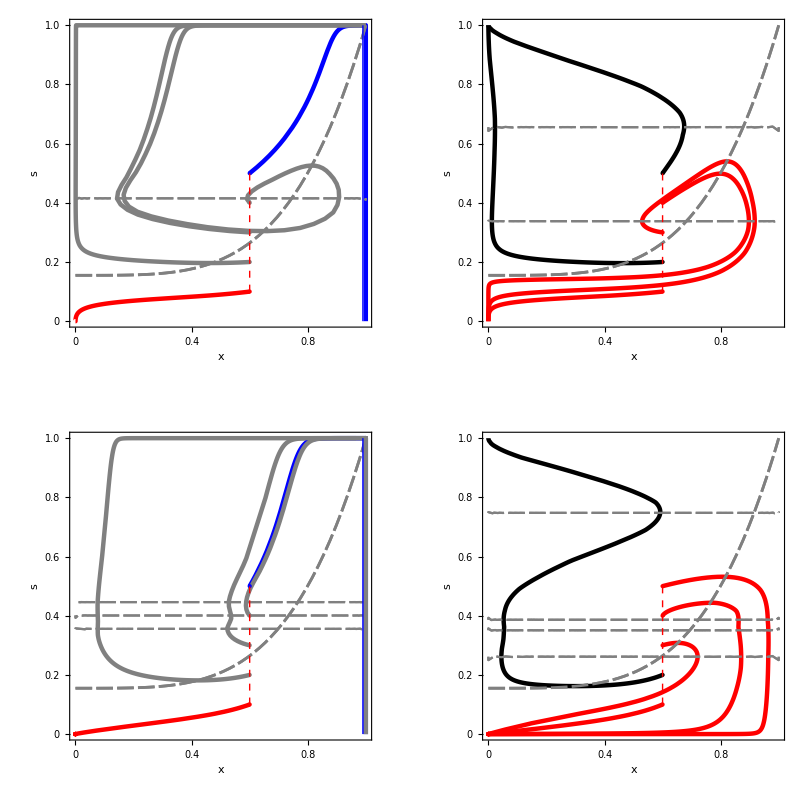

```mathematica
GraphicsGrid[{{pltl, pltr}, {plbl,plbr}},ImageSize->800]
```